```mathematica
LaguerreL[1,2,100]
```

-97

```mathematica
n = Range[0,6];
```

```mathematica
LaguerreL[1,1,  0.1]
```

1.9

```mathematica
overlap[n_, m_, α_]:= If[m≥n,Sqrt[(Factorial[n]/Factorial[m]) α^(m-n) Exp[-Abs[α]^2] LaguerreL[n, (m-n), Abs[α]^2]],(Factorial[m]/Factorial[n]) α^(m-n) Exp[-Abs[α]^2] LaguerreL[m, (n-m), Abs[α]^2]];
```

```mathematica
probability[n_, m_]:= Abs[overlap[n, m, -5.6]]^2;
```

```mathematica
M = N[Array[probability, {50,50}]];
```

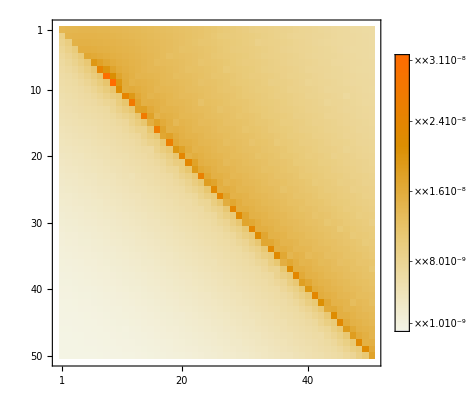

```mathematica
MatrixPlot[M, PlotLegends->True]
```